```mathematica
(*Fluid Mechanics:  A Geometric Point of View*)
```

```mathematica
(*Vector Fields*)
```

## Double Gyre

x (1-0.5 Sin[t])+0.25 x^2 Sin[t]

-1.1 Sin[π y] Sin[π (x (1-0.5 Sin[t])+0.25 x^2 Sin[t])]

{-3.45575 Cos[π y] Sin[π (x (1-0.5 Sin[t])+0.25 x^2 Sin[t])],3.45575 Cos[π (x (1-0.5 Sin[t])+0.25 x^2 Sin[t])] (1-0.5 Sin[t]+0.5 x Sin[t]) Sin[π y]}

6

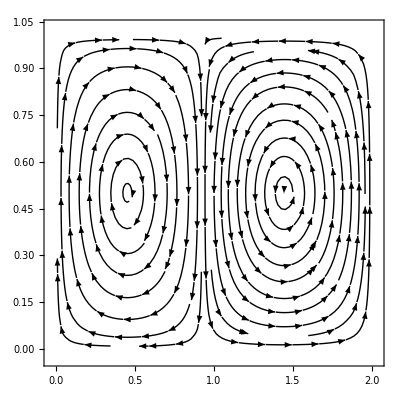

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

DoubleGyre.jpg

3.45575 Cos[π y] Sin[π (x (1-0.5 Sin[t])+0.25 x^2 Sin[t])]

-3.45575 Cos[π (x (1-0.5 Sin[t])+0.25 x^2 Sin[t])] (1-0.5 Sin[t]+0.5 x Sin[t]) Sin[π y]

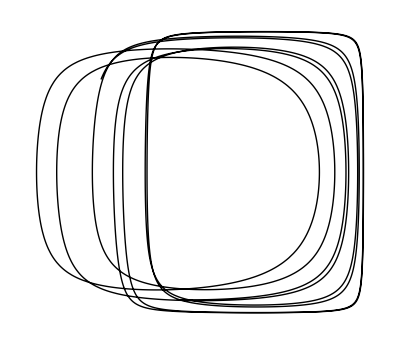

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

IntegralCurveDGyre.jpg

```mathematica
ϵ=0.25;
α=1.1;
a[t_]=ϵ*Sin[t];b[t]=1-2ϵ*Sin[t];
θ[t_,x_]=a[t] x^2+b[t]*x
A[t_,x_,y_]=-α*Sin[Pi*θ[t,x]]*Sin[Pi*y]
V[t_,x_,y_]={D[A[t,x,y],y],-D[A[t,x,y],x]}
T=6
DoubleGyre=StreamPlot[V[T,x,y],{x,0,2},{y,0,1},StreamStyle->{Thick,Black}]

SetDirectory[NotebookDirectory[]]
Export["DoubleGyre.jpg",DoubleGyre,ImageResolution->400]
Vx[t_,x_,y_]=-D[A[t,x,y],y]
Vy[t_,x_,y_]=D[A[t,x,y],x]
s=NDSolve[{x'[t]==Vx[t,x[t],y[t]],y'[t]==Vy[t,x[t],y[t]],x[0]==1+0.1*RandomReal[{-1,1}],y[0]==Random[]},{x,y},{t,20}];
IntegralCurveDGyre=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,10},Axes->False,PlotStyle->{Thick,Black}]

SetDirectory[NotebookDirectory[]]

Export["IntegralCurveDGyre.jpg",IntegralCurveDGyre,ImageResolution->400]
ParametricPlot3D[Evaluate[{x[t],y[t],t}/.s],{t,0,10},Axes->False];
```

## Flow Near a Fixed Point

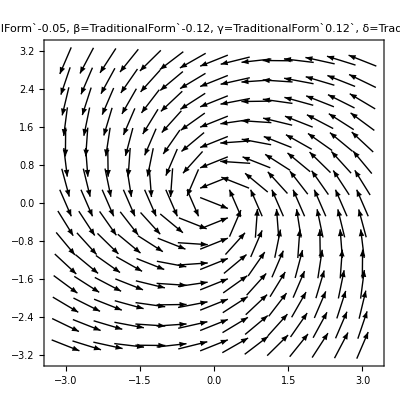

```mathematica
α=RandomReal[{-1,1}];
β=RandomReal[{-1,1}];
γ=RandomReal[{-1,1}];
δ=RandomReal[{-1,1}];
(*β=-5.0; γ=-4.0; α=21.0; δ=32.0;*)

VectorPlot[{(α*x+β*y)/(√((α*x+β*y)^2+(γ*x+δ*y)^2)),(γ*x+δ*y)/(√((α*x+β*y)^2+(γ*x+δ*y)^2))},{x,-3,3},{y,-3,3},PlotLabel->StringForm["α=`1`, β=`2`, γ=`3`, δ=`4`",α,β,γ,δ],VectorStyle->{Thick,Black},BaseStyle->{FontSize->Scaled[.04]}];


α=-0.05;δ=-0.05;γ=0.12;β=-0.12;
VectorPlot[{(α*x+β*y)/(√((α*x+β*y)^2+(γ*x+δ*y)^2)),(γ*x+δ*y)/(√((α*x+β*y)^2+(γ*x+δ*y)^2))},{x,-3,3},{y,-3,3},PlotLabel->StringForm["α=`1`, β=`2`, γ=`3`, δ=`4`",α,β,γ,δ],VectorStyle->{Thick,Black},BaseStyle->{FontWeight->"Bold", FontSize->Scaled[.04]}]
```

## Foliation of a Torus

```mathematica
ω=ContinuedFractionK[1,{n,1,6}]
R=4;
torus=ParametricPlot3D[{Cos[2Pi*x](R+Cos[2Pi*y]),Sin[2Pi*x](R+Cos[2Pi*y]),Sin[2Pi*y]},{x,0,1},{y,0,1},Boxed->False,Mesh->None,Axes->None];
FoliationTorus=ParametricPlot3D[{Cos[2Pi*t](R+Cos[2Pi*ω*t]),Sin[2Pi*t](R+Cos[2Pi*ω*t]),Sin[2Pi*ω*t]},{t,0,50},Mesh->None,Axes->None,Boxed->False,PlotStyle->{Thick,Black}]
SetDirectory[NotebookDirectory[]]

Export["FoliationTorus.jpg",FoliationTorus,ImageResolution->400]
```

8/13

-Graphics3D-

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

FoliationTorus.jpg

## Self-Gravitating Fluids

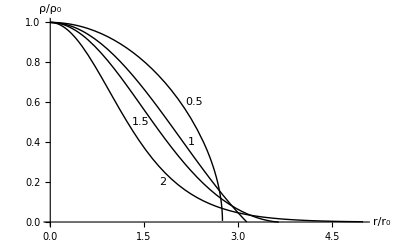

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

SelfGravSphere.jpg

```mathematica
eps=10^-6;
n=0.5;

X=5;
s=NDSolve[{χ''[x]+2/x*χ'[x]==-(Abs[χ[x]])^n,χ[eps]==1,χ'[eps]==0},χ,{x,eps,X}];
p1=Plot[{Evaluate[(χ[x])^n]/.s},{x,eps,X},PlotStyle->{Thick,Black},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"r/r_0","ρ/ρ_0"},PlotLegends->Automatic, PlotRange->All];
t1=Graphics[Text["0.5",{2.3,0.6}]];
Show[p1,t1];
n=1.0000001;

X=5;
s=NDSolve[{χ''[x]+2/x*χ'[x]==-(Abs[χ[x]])^n,χ[eps]==1,χ'[eps]==0},χ,{x,eps,X}];
p2=Plot[{Evaluate[(χ[x])^n]/.s},{x,eps,X},PlotStyle->{Thick,Black},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"r/r_0","ρ/ρ_0"},PlotLegends->Automatic, PlotRange->All];
t2=Graphics[Text["1",{2.25,0.4}]];
n=1.5;

X=5;
s=NDSolve[{χ''[x]+2/x*χ'[x]==-(Abs[χ[x]])^n,χ[eps]==1,χ'[eps]==0},χ,{x,eps,X}];
p3=Plot[{Evaluate[(χ[x])^n]/.s},{x,eps,X},PlotStyle->{Thick,Black},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"r/r_0","ρ/ρ_0"},PlotLegends->Automatic, PlotRange->All];
t3=Graphics[Text["1.5",{1.45,0.5}]];
n=3;

X=5;
s=NDSolve[{χ''[x]+2/x*χ'[x]==-(Abs[χ[x]])^n,χ[eps]==1,χ'[eps]==0},χ,{x,eps,X}];
p4=Plot[{Evaluate[(χ[x])^n]/.s},{x,eps,X},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"r/r_0","ρ/ρ_0"},PlotLegends->Automatic, PlotRange->All,PlotStyle->{Thick,Black}];
t4=Graphics[Text["2",{1.8,0.2}]];
eps=10^-10;
n=0.05;

X=5;
s=NDSolve[{χ''[x]+2/x*χ'[x]==-(Abs[χ[x]])^n,χ[eps]==1,χ'[eps]==0},χ,{x,eps,X}];
p0=Plot[{Evaluate[(χ[x])^n]/.s},{x,eps,X},PlotStyle->Automatic,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"r/r_0","ρ/ρ_0"},PlotLegends->Automatic, PlotRange->All];

SelfGravSphere=Show[p1,p2,p3,p4,t1,t2,t3,t4]
SetDirectory[NotebookDirectory[]]
Export["SelfGravSphere.jpg",SelfGravSphere,ImageResolution->400]
```

## Stirrer in the Upper Half Plane

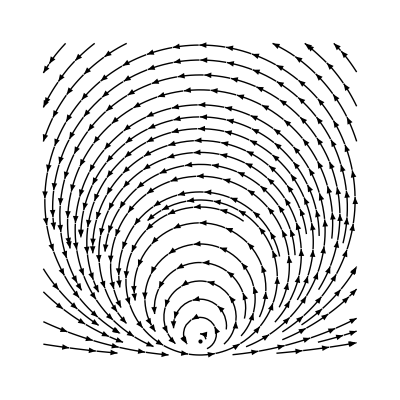

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

StirrerUpperPlane.jpg

```mathematica
(*ζ={RandomReal[{-1,1}], RandomReal[{0,2}]}*)
ζ={0,1};
barζ={ζ[[1]],-ζ[[2]]};
x0=RandomReal[{-10,10}];
y0=RandomReal[{0,10}];
{x0,y0}={-5.527603197878509,2.330338059008586};
v[x_,y_]={(-(y-1))/(x^2+(y-1)^2)-(-(y+1))/(x^2+(y+1)^2),x/(x^2+(y-1)^2)-x/(x^2+(y+1)^2)};
streamplot=StreamPlot[v[x,y],{x,-10,10},{y,0,20},StreamStyle->{Thick,Black},Frame->False];
pointplot=Graphics[{PointSize[Large],Point[{0,1}]}];

curve=ContourPlot[((x-ζ[[1]])^2+(y-ζ[[2]])^2)/((x-barζ[[1]])^2+(y-barζ[[2]])^2)==((x0-ζ[[1]])^2+(y0-ζ[[2]])^2)/((x0-barζ[[1]])^2+(y0-barζ[[2]])^2),{x,-10,10},{y,0,20},ContourStyle->{Thick,Dotted,Black}];
StirrerUpperPlane=Show[streamplot,pointplot]
SetDirectory[NotebookDirectory[]]
Export["StirrerUpperPlane.jpg", StirrerUpperPlane,ImageResolution->400]
{x0,y0};
```

## Stirrer Inside Circle

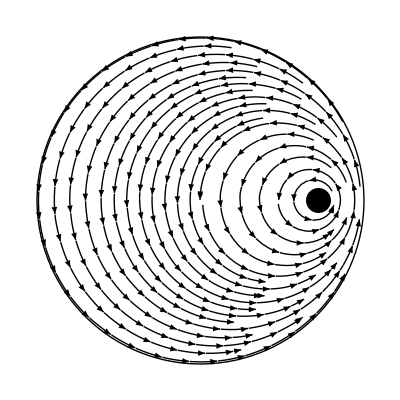

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

StirrerCircle.jpg

```mathematica
(*ζ={RandomReal[{-1,1}], RandomReal[{0,2}]}*)
a=1;
ζv={0.72,0.0};
mirrorζv=1/(ζv[[1]]^2+ζv[[2]]^2){ζv[[1]],ζv[[2]]};
r0=RandomReal[{0,1}];
θ0=RandomReal[{-Pi,Pi}];
x0= r0*Cos[θ0];
y0= r0*Sin[θ0];
{x0,y0}={-0.06024058762060472,0.021847679510982543};
(*((x0-ζ[[1]])^2+(y0-ζ[[2]])^2)/((x0-mirrorζ[[1]])^2+(y0-mirrorζ[[2]])^2)*)
v[x_,y_]={(-(y-ζv[[2]]))/((x-ζv[[1]])^2+(y-ζv[[2]])^2)-(-(y-mirrorζv[[2]]))/((x-mirrorζv[[1]])^2+(y-mirrorζv[[2]])^2),(x-ζv[[1]])/((x-ζv[[1]])^2+(y-ζv[[2]])^2)-(x-mirrorζv[[1]])/((x-mirrorζv[[1]])^2+(y-mirrorζv[[2]])^2)};
streamplot=StreamPlot[v[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},0<x^2+y^2<1],StreamStyle->{Thick,Black}];
circle=Graphics[{Thick,Circle[{0,0},1]}];
pointplot=Graphics[{PointSize[0.045],Point[ζv]}];

curve=ContourPlot[((x-ζv[[1]])^2+(y-ζv[[2]])^2)/((x-mirrorζv[[1]])^2+(y-mirrorζv[[2]])^2)==((x0-ζv[[1]])^2+(y0-ζv[[2]])^2)/((x0-mirrorζv[[1]])^2+(y0-mirrorζv[[2]])^2),{x,-1,1},{y,-1,1},ContourStyle->{Thick,Dotted,Black}];
StirrerCircle=Show[circle,pointplot,streamplot]
{x0,y0};
SetDirectory[NotebookDirectory[]]
Export["StirrerCircle.jpg", StirrerCircle,ImageResolution->400]
```

# Flow Past a Cylinder

{x/(√(x^2+y^2)),y/(√(x^2+y^2))}

{1+(1-(2 x^2)/(x^2+y^2))/(x^2+y^2),-(2 x y)/((x^2+y^2)^2)}

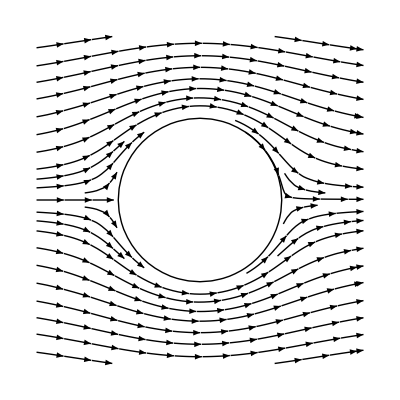

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

FlowPastCylinder.jpg

```mathematica
u={1,0};
a=1;
unit[x_,y_]={x/(√(x^2+y^2)),y/(√(x^2+y^2))}
v[{x_,y_}]=u+a^2/(x^2+y^2)(u-2unit[x,y] x/(√(x^2+y^2)))
velplot=StreamPlot[v[{x,y}],{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},x^2+y^2>1],StreamStyle->{Thin,Black}];
circle=ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2},ContourStyle->{Thick,Black},Frame->None];
FlowPastCylinder=Show[circle,velplot]
SetDirectory[NotebookDirectory[]]
Export["FlowPastCylinder.jpg", FlowPastCylinder,ImageResolution->400]
```

```mathematica
Joukowski Airfoil
```

Airfoil Joukowski

```mathematica
b=0.15;h=0.075;
center={-h,(1+h)b};
radius=(1+h)√(1+b^2);
J1[{x_,y_}]=Through[{Re,Im}[x+I*y+(x-I*y)/(x^2+y^2)]];
J2[{x_,y_}]=Assuming[x>0&&y>0,Simplify[J1[{x,y}]]];
J[{x_,y_}]=J2[center+radius*{x,y}];

Jplot=ParametricPlot[J[{Cos[θ],Sin[θ]}],{θ,0,2Pi},Axes->False]/.l_Line:>{EdgeForm[Directive[AbsoluteThickness[3],Black]],Gray,FilledCurve[l]}

Off[Solve::ratnz]
Solve[r*z+c+1/(r*z+c)==w,z];
c=-h+I*(1+h)b;
r=radius;


K[z_]=(-2 c r+r z-r √(-4+z^2))/(2 r^2);
Clear[v,V,vK]
v[z_]=1-1/z^2;
vK[z_]=Simplify[v[K[z]]K'[z]];
V[x_,y_]=Through[{Re,Im}[Conjugate[v[x+I*y]]]];
Vplot=StreamPlot[V[x,y],{x,-2,2},{y,-2,2}];
vK[x_,y_]=Through[{Re,Im}[Conjugate[vK[x+I*y]]]];
vKplot=StreamPlot[vK[x,y],{x,-2,2},{y,-2,2},StreamPoints->20,Frame->None,StreamStyle->{Thin,Black}];
{r,c}
Joukowski=Show[vKplot,Jplot]
SetDirectory[NotebookDirectory[]]
Export["Joukowski.jpg",Joukowski,ImageResolution->400]
```

-Graphics-

{1.08703,-0.075+0.16125 ⅈ}

-Graphics-

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

Joukowski.jpg

Surface Waves

√(k Tanh[k])

(k Sech[k]^2+Tanh[k])/(2 √(k Tanh[k]))

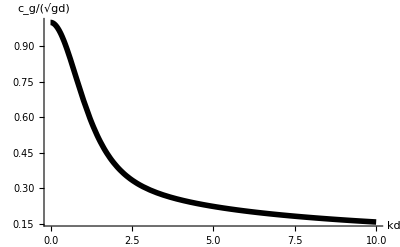

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

GroupVelocity.jpg

1/2 (Csch[k] Sech[k] √((k+O[1/k]^2) Tanh[k])+(1/k+O[1/k]^4) √((k+O[1/k]^2) Tanh[k]))

```mathematica
Surface Waves
Clear[ω]
ω[k_]=√(g*k*Tanh[k*d])
v[k_]=D[ω[k],k]
g=1;
d=1;
GroupVelocity=Plot[{v[k]},{k,0,10},AxesOrigin->{0,0},PlotStyle->{{Thickness[0.01],Black}}, AxesLabel->{"kd","c_g/(√gd)"},PlotRange->All]
SetDirectory[NotebookDirectory[]]
Export["GroupVelocity.jpg",GroupVelocity,ImageResolution->400]


Series[v[k],{k,Infinity,1}]
```

## Shocks in the Burgers Equation

1/2+1/(1+x^2)

((1+x^2) (-1+3 x^2))/(2 x^2)

{0.57735,1.5396}

{-0.500149}

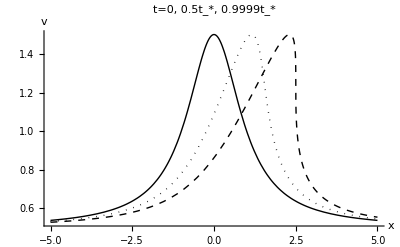

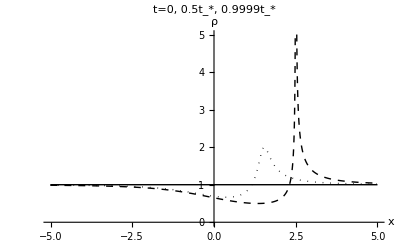

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

ShockBurgersVelocity.jpg

ShockBurgersDensity.jpg

0.47735

1.6396

x/2+ArcTan[x]

1.46415

-0.0725334

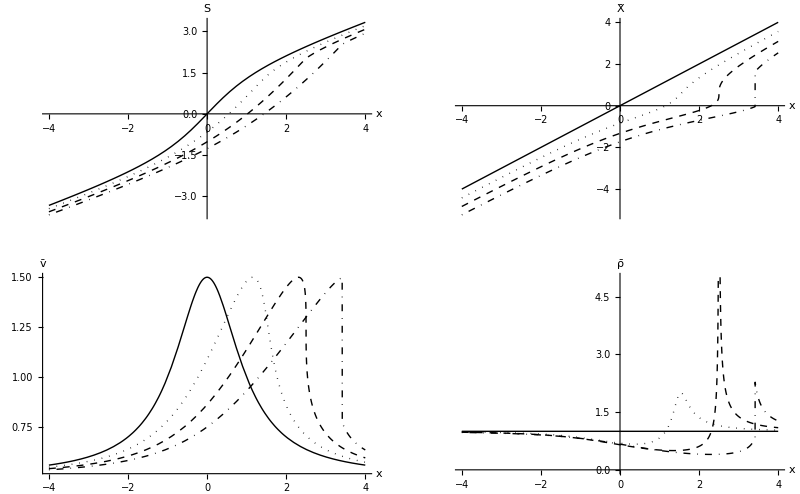

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

ShockMaxwellRule.jpg

```mathematica
Clear[u]
u[x_]=1/2+1/(1+x^2)
Factor[D[((1+x^2)^2)/(2 x),x]]
N[{1/(√3),(1+1/3)^2/(2*1/(√3))}]
Minimize[{((1+x^2)^2)/(2 x),x>0},x];
Plot[First[t/.Solve[1+u'[x]t==0,t]],{x,0,1}];
Plot[u[x],{x,-1,1},PlotRange->All];
Plot[{-1/u'[x]},{x,-1,1},PlotRange->All];
Off[FindRoot::lstol]
Xs[x_,t_]:=Simplify[X/.NSolve[x==X+u[X]*t,X,Reals]]
Xs[1/(√3)+u[1/(√3)]*8/(3 √3)*1.00000001,8/(3 √3)*1.5]


X[x_,t_]:=xx/.FindRoot[x==xx+u[xx]*t,{xx,x},Evaluated->False]
v[x_,t_]:=u[X[x,t]];
ρ[x_,t_]:=1/(1+u'[X[x,t]]t);
ρ[-0.1,0.2];
tstar=8/(3 √3);
xstar=1/(√3);
Plot[{ρ[x,0],ρ[x,0.5tstar],ρ[x,0.9999*tstar]},{x,-2,2},PlotRange->All];
ShockBurgersVelocity=Plot[{v[x,0],v[x,0.5tstar],v[x,0.9999*tstar]},{x,-5,5},AxesLabel->{x,v},PlotLabel->"t=0, 0.5t_*, 0.9999t_*",GridLines->{{0,1/(√3)},{0,u[1/(√3)],u[0]}},PlotRange->All,
PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed}}]
ShockBurgersDensity=Plot[{ρ[x,0],ρ[x,0.5tstar],ρ[x,0.9999*tstar]},{x,-5,5},AxesLabel->{x,ρ},PlotLabel->"t=0, 0.5t_*, 0.9999t_*",PlotRange->{0,5},
PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed}}]
SetDirectory[NotebookDirectory[]]
Export["ShockBurgersVelocity.jpg",ShockBurgersVelocity,ImageResolution->400]
Export["ShockBurgersDensity.jpg",ShockBurgersDensity,ImageResolution->400]

Plot[{ρ[x,0]v[x,0],ρ[x,0.5tstar]v[x,0.5tstar],ρ[x,0.9999*tstar]v[x,0.999*tstar]},{x,-5,5},AxesLabel->{x,ρv},PlotLabel->"t=0, 0.5t_*, 0.9999t_*",PlotRange->{0,5},
PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed}}];



x1=xstar-0.1
t1=tstar+0.1
S0[x_]=Integrate[u[x],x]
Sbar[x_,t_]:=First[NMinimize[(x-a)^2/(2t)+S0[a],a]]
Xbar[x_,t_]:=a/.NMinimize[(x-a)^2/(2t)+S0[a],a][[2]]
vbar[x_,t_]:=u[Xbar[x,t]]
ρbar[x_,t_]:=1/(1+u'[Xbar[x,t]]t);
vbar[0.1,0.2]

Sbar[0.1,0.2]
Splot=Plot[{S0[x],Sbar[x,0.5tstar],Sbar[x,tstar],Sbar[x,1.5tstar]},{x,-4,4},PlotRange->All,AxesLabel->{"x",S̄},PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed},{Thick,Black, DotDashed}}];
Xplot=Plot[{x,Xbar[x,0.5tstar],Xbar[x,tstar],Xbar[x,1.5tstar]},{x,-4,4},PlotRange->All,AxesLabel->{"x",X̄},PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed},{Thick,Black, DotDashed}}];
vplot=Plot[{u[x],vbar[x,0.5tstar],vbar[x,tstar],vbar[x,1.5tstar]},{x,-4,4},PlotRange->All,AxesLabel->{"x",v̄},PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed},{Thick,Black, DotDashed}}];
ρplot=Plot[{1,ρbar[x,0.5tstar],ρbar[x,tstar],ρbar[x,1.5tstar]},{x,-4,4},PlotRange->{0,5},AxesLabel->{"x",ρ̄},PlotStyle->{{Thick,Black},{Thick,Black,Dotted},{Thick,Black,Dashed},{Thick,Black, DotDashed}}];

ShockMaxwellRule=GraphicsGrid[{{Splot,Xplot},{vplot,ρplot}}]
SetDirectory[NotebookDirectory[]]
Export["ShockMaxwellRule.jpg",ShockMaxwellRule,ImageResolution->400]
```

## Boundary Layer

{{g→InterpolatingFunction[{{0., 20.}}, <>]}}

0.692475

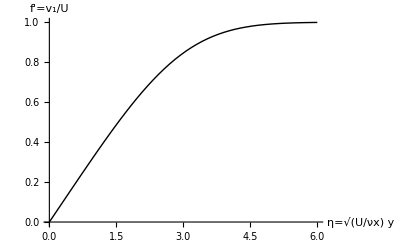

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

BlasiusSolution.jpg

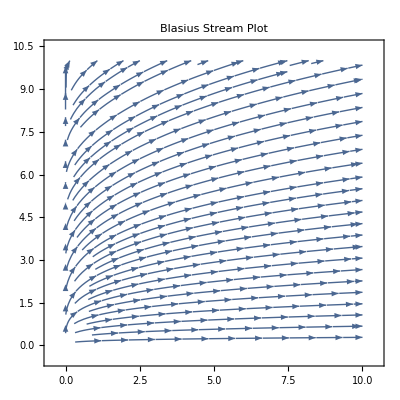

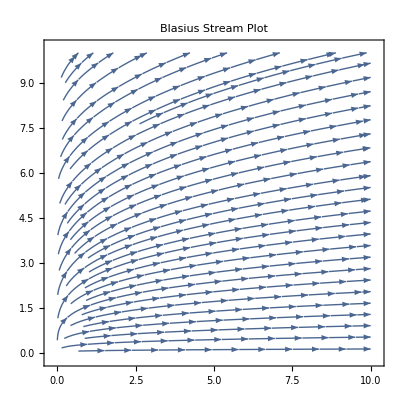

1

ⅇ^(-y^3/12)

(2/3)^(2/3) Gamma[1/3]

(3/2)^(1/3)/(√Gamma[1/3])

0.699384

1/3 y^2 ExpIntegralE[1/3,y^3/12]-1/3 y^2 ExpIntegralE[2/3,y^3/12]+(2/3)^(2/3) y Gamma[1/3]-2 (2/3)^(1/3) Gamma[2/3]

1/3 y^2 1/3y^3/12-1/3 y^2 2/3y^3/12+(2/3)^(2/3) y 1/3-2 (2/3)^(1/3) 2/3

(y^2 1/3y^3/(8 (1/3)^(3/2))-y^2 2/3y^3/(8 (1/3)^(3/2))+2 y (1/3)^(3/2)-4 1/3 2/3)/(2 (1/3)^(3/2))

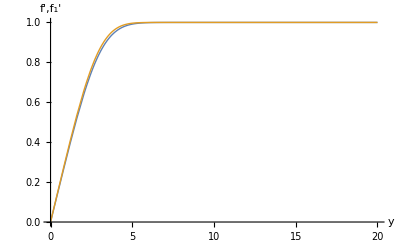

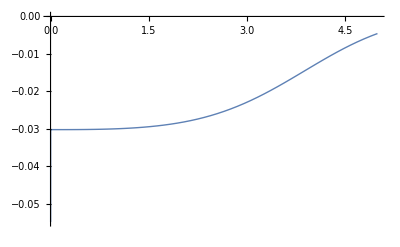

```mathematica
Clear[g]
m=0;
s=NDSolve[{g'''[η]+(m+1)/2 g[η]g''[η]==0,g[0]==0,g'[0]==0,g''[0]==1},g,{η,0,20}]
Plot[Evaluate[g'[η]/.s],{η,0,5},PlotStyle->Automatic];
a=1/(√(Evaluate[g'[20]/.s][[1]]))
f[η_]:=a*Evaluate[g[a*η]/.s][[1]]
BlasiusSolution=Plot[f'[η],{η,0,6},PlotStyle->{Black,Thick},AxesOrigin->{0,0},AxesLabel->{"η=√(U/νx) y","f'=v_1/U"},AxesLabel->{"η","f"}]
SetDirectory[NotebookDirectory[]]
Export["BlasiusSolution.jpg",BlasiusSolution,ImageResolution->400]
f1[η_]=f'[η];
u[x_,y_]=f1[y/(√x)];
v[x_,y_]=1/(2 √x)(-f[y/(√x)]+y/(√x)*f1[y/(√x)]);
VectorPlot[{{u[x,y],v[x,y]}},{x,0.00001,10},{y,0.00001,10},StreamPoints->1000,AxesOrigin->{0,0},PlotLabel->"Blasius Stream Plot"]
StreamPlot[{{u[x,y],v[x,y]}},{x,0.00001,10},{y,0.00001,10},StreamPoints->1000,AxesOrigin->{0,0},PlotLabel->"Blasius Stream Plot"]
(*Weyl's Approximation*)
h0[y_]=1
h1[y_]=Exp[-1/4 Integrate[h0[y1](y-y1)^2,{y1,0,y}]]
(*h2[y_]=Exp[-1/4 Integrate[h1[z](y-z)^2,{z,0,y}]]*)
c1=Integrate[h1[y],{y,0,Infinity}]
(*c2=NIntegrate[h2[y],{y,0,Infinity}]*)
a1=1/(√c1)
N[a1]

g1[y_]=Integrate[(y-u)*h1[u],{u,0,y}]
g1[y]//TraditionalForm
f1[y_]=Simplify[a1*g1[a1*y]];
f1[y]//TraditionalForm
Plot[{f'[η],f1'[η]},{η,0,20},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"y","f',f_1'"}]
Plot[{(f'[η]-f1'[η])/f'[η]},{η,0,5},PlotStyle->Thick,AxesOrigin->{0,0}]
```

## Transients

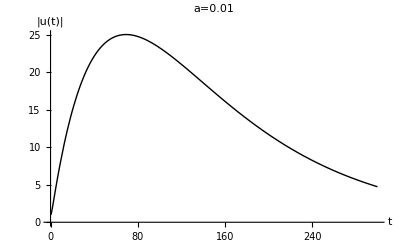

/Users/saradrajeev1/Desktop/Draft4/ImagesPrograms

Transient.jpg

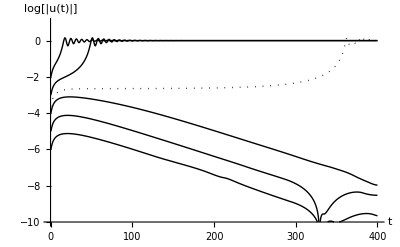

/Users/saradrajeev1/Desktop/Draft4/ImagesPrograms

TransientNonLinear.jpg

```mathematica
Clear[f]
a=0.01;
f[t_]=Sqrt[Exp[-2a*t]+1/a^2(Exp[-a*t]-Exp[-2a*t])^2];
Transient=Plot[f[t],{t,0,3/a},PlotLabel->"a=0.01",AxesLabel->{t,"|u(t)|"},PlotStyle->{Thick,Black}]
SetDirectory[NotebookDirectory[]]
Export["Transient.jpg",Transient,ImageResolution->400]
a=1/30.;
eps=10^-6;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p1=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Thick, Black},AxesLabel->{t,"log[|u(t)|]"}];
eps=10^-5;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p2=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Thick, Black},AxesLabel->{t,"log[|u(t)|]"}];
eps=10^-4;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p3=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Thick, Black},AxesLabel->{t,"log[|u(t)|]"}];
eps=2.445*10^-4;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p4=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Dotted,{Thick, Black}},AxesLabel->{t,"log[|u(t)|]"}];
eps=10^-3;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p5=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Thick, Black},AxesLabel->{t,"log[|u(t)|]"}];
eps=10^-2;
s=NDSolve[{u1'[t]==-a*u1[t]+√((u1[t])^2+(u2[t])^2)*u2[t],u2'[t]==u1[t]-2a*u2[t]-√((u1[t])^2+(u2[t])^2)*u1[t],u1[0]==eps,u2[0]==0},{u1,u2},{t,500}];
p6=Plot[Evaluate[Log[10,√((u1[t])^2+(u2[t])^2)]/.s],{t,0,400},PlotRange->{{0,400},{-10,1}},AxesOrigin->{0,-10},PlotStyle->{Thick, Black},AxesLabel->{t,"log[|u(t)|]"}];
TransientNonLinear=Show[p1,p2,p3,p4,p5,p6]
SetDirectory[NotebookDirectory[]]
Export["TransientNonLinear.jpg",TransientNonLinear,ImageResolution->400]
```

```mathematica
Animated Kapitza Pendulum
```

Animated Kapitza Pendulum

Modified  by S. G. Rajeev from a code for an animated pendulum 
(on the Mathematica web site) by Joel Frederico,  Rob Morris and Fernand Brunschwig

```mathematica
Manipulate[
Module[{eqns,soln,θ,θin},
θin=θ0;

eqns={θ''[t]+g/L*Sin[θ[t]]==Ω^2*A0*Sin[Ω*t]*Cos[θ[t]]-Ω^2*B0*Sin[Ω*t]*Sin[θ[t]],θ'[0]==0,θ[0]==θ0};
soln=NDSolve[eqns,{θ[t]},{t,p-1,p},MaxSteps->100000];

With[{A=Evaluate[A0*Cos[Ω*t]/.{t->p}],
        B=Evaluate[B0*Sin[Ω*t]/.{t->p}],
sina=Sin[Evaluate[θ[t]/.soln[[1]]]/.{t->p}],mgL=m g L,cosm=Cos[θ0],cosa=Cos[Evaluate[θ[t]/.soln[[1]]]/.{t->p}]},
Grid[{{
      Graphics[{Point[{0,0}],    
{Thickness[0.02],Black, Line[{{0,0},{A,B}}]},
Line[{{A,B},L {sina,-cosa}}],
{Darker[Black,.2],Disk[L {sina,-cosa},Sqrt[m/20]]},
Dotted,Black,
Line[{{0,0},L {-Sin[Pi-θ0],Cos[Pi-θ0]}}],
Line[{{0,0},L {Sin[Pi-θ0],Cos[Pi-θ0]}}],
Circle[{0,0},L,{(3 Pi/2)-θ0,(3 Pi/2)+θ0}],
Line[{{0,0},{0,-L}}]
},PlotRange->4,ImageSize->{275,300}]}}]]
],
Style["Initial Conditions and Parameters",Bold],

{{Ω,100.0,"Frequency of support Ω"},0.0,200.0,Appearance->"Labeled"},
{{A0,0.001,"Horizontal amplitude of support A0"},.00,0.1,Appearance->"Labeled"},
{{B0,0.1,"Vertical amplitude of support B0"},0.0,0.2,Appearance->"Labeled"},
{{θ0,0.9*Pi,"Initial angle θ0 "},-0.999*Pi,0.999*Pi,Appearance->"Labeled"},
{{L,2,"length L"},.1,3,Appearance->"Labeled"},
{{m,2.5,"mass m"},.1,5,Appearance->"Labeled"},
{{g,9.8,"gravity g"},1,20, Appearance->"Labeled"},
Delimiter,{{p,0,"animate"},0,Infinity,ControlType->Trigger},
AutorunSequencing->{1,2,3},TrackedSymbols->True,SynchronousUpdating->False
]
```

# KdV

```mathematica
c=6;
b=1/2 c;
a=2/3 c;
Lψ[x_]=D[ψ[x],{x,2}]+ϕ[x]*ψ[x]
Pψ[x_]=a*D[ψ[x],{x,3}]+b*D[ϕ[x],x]*ψ[x]+c*ϕ[x]D[ψ[x],x]
PLψ[x_]=a*D[Lψ[x],{x,3}]+b*D[ϕ[x],x]*Lψ[x]+c*ϕ[x]D[Lψ[x],x]
LPψ[x_]=D[Pψ[x],{x,2}]+ϕ[x]*Pψ[x]
Simplify[PLψ[x]-LPψ[x]]
```

ϕ[x] ψ[x]+ψ''[x]

3 ψ[x] ϕ'[x]+6 ϕ[x] ψ'[x]+4 ψ^(3)[x]

3 ϕ'[x] (ϕ[x] ψ[x]+ψ''[x])+6 ϕ[x] (ψ[x] ϕ'[x]+ϕ[x] ψ'[x]+ψ^(3)[x])+4 (3 ψ'[x] ϕ''[x]+3 ϕ'[x] ψ''[x]+ψ[x] ϕ^(3)[x]+ϕ[x] ψ^(3)[x]+ψ^(5)[x])

12 ψ'[x] ϕ''[x]+15 ϕ'[x] ψ''[x]+3 ψ[x] ϕ^(3)[x]+6 ϕ[x] ψ^(3)[x]+ϕ[x] (3 ψ[x] ϕ'[x]+6 ϕ[x] ψ'[x]+4 ψ^(3)[x])+4 ψ^(5)[x]

ψ[x] (6 ϕ[x] ϕ'[x]+ϕ^(3)[x])

## Vortex Filament

```mathematica
Clear[ν,τ0]
μ=ν^2/(ν^2+τ0^2)
η[s_,t_]=ν(s-2τ0*t)
Θ[s_,t_]=τ0*s+(ν^2-τ0^2)t
r[s_,t_]=2 μ/ν Sech[η[s,t]]
ξ[s_,t_]={s-2 μ/ν Tanh[η[s,t]],r[s,t]Cos[Θ[s,t]],r[s,t]Sin[Θ[s,t]]}
TraditionalForm[MatrixForm[ξ[s,t]]]
ν=1.1;
τ0=0.8;
Manipulate[ParametricPlot3D[ξ[s,t],{s,-4,8},Boxed->False,Axes->False],{t,0,2}]
HasimotoVortexFilamentSoliton=ParametricPlot3D[ξ[s,1.4],{s,-4,8},PlotStyle->{Black,Thick},Boxed->False,Axes->False]
SetDirectory[NotebookDirectory[]]
Export["HasimotoVortexFilamentSoliton.jpg",HasimotoVortexFilamentSoliton,ImageResolution->400]
```

ν^2/(ν^2+τ0^2)

ν (s-2 t τ0)

s τ0+t (ν^2-τ0^2)

(2 ν Sech[ν (s-2 t τ0)])/(ν^2+τ0^2)

{s-(2 ν Tanh[ν (s-2 t τ0)])/(ν^2+τ0^2),(2 ν Cos[s τ0+t (ν^2-τ0^2)] Sech[ν (s-2 t τ0)])/(ν^2+τ0^2),(2 ν Sech[ν (s-2 t τ0)] Sin[s τ0+t (ν^2-τ0^2)])/(ν^2+τ0^2)}

(s-(2 ν tanh(ν (s-2 t τ0)))/(ν^2+τ0^2)
(2 ν cos(s τ0+t (ν^2-τ0^2)) sech(ν (s-2 t τ0)))/(ν^2+τ0^2)
(2 ν sin(s τ0+t (ν^2-τ0^2)) sech(ν (s-2 t τ0)))/(ν^2+τ0^2))

-Graphics3D-

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

HasimotoVortexFilamentSoliton.jpg

## (*Spectral Methods*)

```mathematica
Clear[T,Chebint,Cheb]
T[k_,x_]=ChebyshevT[k,x];
Tp[k_,x_]=D[T[k,x],x];
(*
Tppraw[x_]=D[T[k,x],{x,2}];
Tpp[k_,x_]=Which[Abs[x]≠1,Tppraw[x],x==-1,(-1)^k/3 k^2(k^2-1),x==1,1/3 k^2(k^2-1)];
(*To avoid the spurious singularity at Abs[x]=1*)
*)
Ti[k_,x_]=If[k≠1,1/2 (-ChebyshevT[-1+k,x]/(-1+k)+ChebyshevT[1+k,x]/(1+k))-(k Sin[(k π)/2])/(1-k^2)ChebyshevT[0,x],(ChebyshevT[2,x]+ChebyshevT[0,x])/4];
(*To avoid the singularity for k=1*)


x[k_,n_]=N[Cos[k*Pi/n]];
Cheb[n_]:=Table[N[T[k,x[j,n]]],{j,0,n},{k,0,n}]
Chebp[n_]:=Table[N[Tp[k,x[j,n-1]]],{j,0,n-1},{k,0,n}]
xCheb[n_]:=Table[N[x[j,n+1]*T[k,x[j,n+1]]],{j,0,n+1},{k,0,n}]
(*Chebpp[n_]:=Table[N[Tpp[k,x[j,n]]],{j,0,n},{k,0,n}]*)
Chebint[n_]:=Table[N[Ti[k,x[j,n+1]]],{j,0,n+1},{k,0,n}]
P[x_,n_]:=Table[N[T[k,x]],{k,0,n}].Inverse[Cheb[n]]
diff[n_]:=N[Chebp[n]].Inverse[N[Cheb[n]]]
integral[n_]:=Chebint[n].Inverse[Cheb[n]]
Flip[n_]:=Table[If[j==n-k,1,0],{j,0,n},{k,0,n}]
c[n_]:=Table[1,{i,0,n}]
Id[m_,n_]:=Table[N[P[x[k,n-m],n]],{k,0,n-m}]
diff[4,n_]:=diff[n-3].diff[n-2].diff[n-1].diff[n]
diff[2,n_]:=diff[n-1].diff[n]
X[n_]:=N[xCheb[n]].Inverse[N[Cheb[n]]]

(*Chop[Id[1,9]]//MatrixForm*)
```

```mathematica
diff[3]//MatrixForm
Chop[diff[3].integral[2]]//MatrixForm
```

(3.16667 | -4. | 1.33333 | -0.5
-0.166667 | 1.33333 | -1.33333 | 0.166667
0.5 | -1.33333 | 4. | -3.16667)

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

### (*Driven Damped Harmonic Oscillator*)

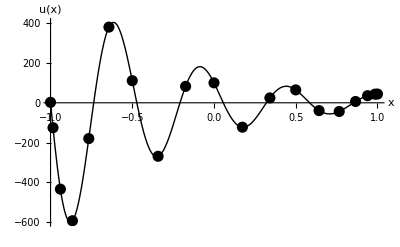

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

DDHOSpectral.jpg

```mathematica
n1=18;
ω=12.0;Ω=15.1;γ=3.0;
L=diff[n1-1].diff[n1]+γ*Id[1,n1-1].diff[n1]+ω^2*Id[2,n1];
α=2.3;β=1.1;
f[x_]=Exp[8*x]*Sin[Ω*x];
fs=Table[N[f[x[k,n1-2]]],{k,0,n1-2}];
A=Join[L,{P[-1,n1]},{P[1,n1-1].diff[n1]}];
b=Join[fs,{α},{β}];
us=Inverse[A].b;
usample=Table[{x[k,n1],us[[k+1]]},{k,0,n1}];
u[x_]=P[x,n1].us;
plotu=Plot[u[x],{x,-1,1},AxesOrigin->{-1,0},PlotStyle->{Thick,Black},AxesLabel->{"x","u(x)"}];
plotusample=ListPlot[usample,PlotStyle->{Black,PointSize[0.02]}];
DDHOSpectral=Show[plotu,plotusample]
SetDirectory[NotebookDirectory[]]
Export["DDHOSpectral.jpg",DDHOSpectral,ImageResolution->400]
```

### (*Standing Waves*)

```mathematica
n1=15;
Table[N[-1/4(Pi*n)^2],{n,1,20}]
A=diff[2,n1];
B=Id[2,n1];
Π=Transpose[NullSpace[{P[1,n1],P[-1,n1]}]];
L=A.Π;
M=B.Π;
Reverse[Eigenvalues[{L,M}]]

Π=Transpose[NullSpace[{P[1,n1],P[-1,n1-1].diff[n1]}]];
L=A.Π;
M=B.Π;
Reverse[Eigenvalues[{L,M}]]
Table[N[-(Pi/2*(n+1/2))^2],{n,0,20}]
```

{-2.4674,-9.8696,-22.2066,-39.4784,-61.685,-88.8264,-120.903,-157.914,-199.859,-246.74,-298.556,-355.306,-416.991,-483.611,-555.165,-631.655,-713.079,-799.438,-890.732,-986.96}

{-2.4674,-9.8696,-22.2066,-39.4784,-61.6884,-88.7312,-122.857,-152.891,-260.471,-285.245,-1123.65,-1188.1,∞,∞}

{-0.61685,-5.55165,-15.4213,-30.2257,-49.9649,-74.6425,-104.321,-139.391,-185.615,-273.223,-485.26,-1155.84,-5039.52,∞}

{-0.61685,-5.55165,-15.4213,-30.2257,-49.9649,-74.6389,-104.248,-138.791,-178.27,-222.683,-272.031,-326.314,-385.531,-449.684,-518.771,-592.793,-671.75,-755.642,-844.468,-938.229,-1036.93}

### (*Orr-Sommerfeld*)

{-0.0000781912-0.261568 ⅈ,-0.0462037-0.953433 ⅈ,-0.0462428-0.953459 ⅈ,-0.0576717-0.322964 ⅈ,-0.082987-0.916133 ⅈ,-0.0830888-0.916215 ⅈ,-0.119744-0.878783 ⅈ,-0.119927-0.878959 ⅈ,-0.154832-0.404415 ⅈ,-0.156482-0.841374 ⅈ,-0.156758-0.841691 ⅈ,-0.162184-0.483741 ⅈ,-0.193204-0.803879 ⅈ,-0.193586-0.804409 ⅈ,-0.208039-0.228413 ⅈ,-0.229702-0.766237 ⅈ,-0.230442-0.767103 ⅈ,-0.233199-0.256095 ⅈ,-0.240183-0.620569 ⅈ,-0.246536-0.554942 ⅈ,-0.264545-0.73032 ⅈ,-0.267444-0.729352 ⅈ,-0.270769-0.44582 ⅈ,-0.297951-0.688845 ⅈ,-0.303888-0.704538 ⅈ,-0.305994-0.461845 ⅈ,-0.322595-0.617626 ⅈ,-0.331468-0.679351 ⅈ,-0.358081-0.627198 ⅈ,-0.358295-0.68355 ⅈ,-0.392378-0.674729 ⅈ,-0.422236-0.674283 ⅈ,-0.453514-0.672735 ⅈ,-0.485052-0.672309 ⅈ,-0.517171-0.671637 ⅈ,-0.550176-0.671326 ⅈ,-0.583774-0.670805 ⅈ,-0.618263-0.670595 ⅈ,-0.653409-0.670133 ⅈ,-0.689395-0.669968 ⅈ,-0.726014-0.669607 ⅈ,-0.763733-0.669771 ⅈ,-0.802567-0.668666 ⅈ,-0.839361-0.667593 ⅈ,-0.877542-0.673524 ⅈ,-0.941757-0.692044 ⅈ,-0.949693-0.652485 ⅈ,-0.953135-0.645306 ⅈ,-1.01891-0.749452 ⅈ,-1.07382-0.590499 ⅈ,-1.07403-0.592579 ⅈ,-1.09444-0.816573 ⅈ,-1.20693-0.910229 ⅈ,-1.21301-0.533837 ⅈ,-1.21428-0.536197 ⅈ,-1.37602-0.477842 ⅈ,-1.37845-0.480124 ⅈ,-1.57154-0.42286 ⅈ,-1.5749-0.424648 ⅈ,-1.81166-0.369069 ⅈ,-1.81567-0.370328 ⅈ,-2.11379-0.316886 ⅈ,-2.11837-0.317725 ⅈ,-2.50439-0.266964 ⅈ,-2.50959-0.267491 ⅈ,-3.02501-0.220034 ⅈ,-3.03103-0.220331 ⅈ,-3.7438-0.176759 ⅈ,-3.75094-0.176884 ⅈ,-4.77847-0.137651 ⅈ,-4.78726-0.137646 ⅈ,-6.34708-0.103068 ⅈ,-6.35839-0.102967 ⅈ,-8.89182-0.0732594 ⅈ,-8.90727-0.0730848 ⅈ,-13.4262-0.048401 ⅈ,-13.4491-0.0481725 ⅈ,-22.7148-0.0286285 ⅈ,-22.7528-0.0283611 ⅈ,-46.687-0.0140427 ⅈ,-46.764-0.0137497 ⅈ,-144.399-0.00472366 ⅈ,-144.628-0.00442005 ⅈ,-2198.34-0.000930918 ⅈ,-2203.19-0.000787783 ⅈ,-6977.84+0.001298 ⅈ,-6987.22+0.000700818 ⅈ}

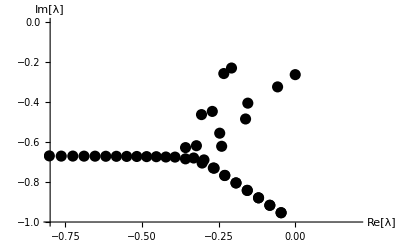

/Users/saradrajeev1/Dropbox/Draft3/ImagesPrograms

OrrSommerfeld90.jpg

```mathematica
(*Setting up Chebychev interpolation*)
T[k_,x_]=ChebyshevT[k,x];
Tp[k_,x_]=D[T[k,x],x];
(*
Tppraw[x_]=D[T[k,x],{x,2}];
Tpp[k_,x_]=Which[Abs[x]≠1,Tppraw[x],x==-1,(-1)^k/3 k^2(k^2-1),x==1,1/3 k^2(k^2-1)];
(*To avoid the spurious singularity at Abs[x]=1*)
*)
Ti[k_,x_]=If[k≠1,1/2 (-ChebyshevT[-1+k,x]/(-1+k)+ChebyshevT[1+k,x]/(1+k))-(k Sin[(k π)/2])/(1-k^2)ChebyshevT[0,x],(ChebyshevT[2,x]+ChebyshevT[0,x])/4];
(*To avoid the singularity for k=1*)

x[k_,n_]=N[Cos[k*Pi/n]];
Cheb[n_]:=Table[N[T[k,x[j,n]]],{j,0,n},{k,0,n}]
Chebp[n_]:=Table[N[Tp[k,x[j,n-1]]],{j,0,n-1},{k,0,n}]
xCheb[n_]:=Table[N[x[j,n+1]*T[k,x[j,n+1]]],{j,0,n+1},{k,0,n}]
(*Chebpp[n_]:=Table[N[Tpp[k,x[j,n]]],{j,0,n},{k,0,n}]*)
Chebint[n_]:=Table[N[Ti[k,x[j,n+1]]],{j,0,n+1},{k,0,n}]
P[x_,n_]:=Table[N[T[k,x]],{k,0,n}].Inverse[Cheb[n]]
diff[n_]:=N[Chebp[n]].Inverse[N[Cheb[n]]]
integral[n_]:=Chebint[n].Inverse[Cheb[n]]
Flip[n_]:=Table[If[j==n-k,1,0],{j,0,n},{k,0,n}]
c[n_]:=Table[1,{i,0,n}]
Id[m_,n_]:=Table[N[P[x[k,n-m],n]],{k,0,n-m}]
diff[4,n_]:=diff[n-3].diff[n-2].diff[n-1].diff[n]
diff[2,n_]:=diff[n-1].diff[n]
X[n_]:=N[xCheb[n]].Inverse[N[Cheb[n]]]

(*Chop[Id[1,9]]//MatrixForm*)
R=5772;
n1=90;
V[x_]=1-x^2;
Vpp=-2;

(*V[x_]=0;
Vpp=0;
*)
Vs=Table[V[x[k,n1-4]],{k,0,n1-4}];
Vmat=DiagonalMatrix[Vs];

A=1/R(diff[4,n1]-2Id[2,n1-2].diff[2,n1]+Id[4,n1])-2*I*Id[4,n1]-I*Vmat.(Id[2,n1-2].diff[2,n1]-Id[4,n1]);
B=(Id[2,n1-2].diff[2,n1]-Id[4,n1]);
Π=Transpose[NullSpace[{P[1,n1],P[-1,n1],P[-1,n1-1].diff[n1],P[1,n1-1].diff[n1]}]];

Dimensions[Π];
Dimensions[A];
L=A.Π;
M=B.Π;

λs=Eigenvalues[{L,M}];
SortBy[λs,Re[-#] &]

OrrSommerfeld90=ListPlot[{Re[#],Im[#]}&/@ λs,AxesOrigin->{-0.8,-1},PlotRange->{{-0.8,0.2},{-1,0}},PlotStyle->{Black,PointSize[0.02]}, AxesLabel->{"Re[λ]","Im[λ]"}]
SetDirectory[NotebookDirectory[]]
Export["OrrSommerfeld90.jpg",OrrSommerfeld90,ImageResolution->400]
```

## (*Finite Difference Method*)

## (*One Dimension*)

```mathematica
Clear[h]
Series[(u[x+h]-u[x])/h,{h,0,1}]
Series[(u[x+h]-2u[x]+u[x-h])/h^2,{h,0,2}]

Series[u[x+h]-(u[x]+h(23u'[x]-16u'[x-h]+5u'[x-2h])/12),{h,0,4}]

Clear[h]
appr=PadeApproximant[z^-2 Log[z]/h,{z,1,{1,2}}]
CoefficientList[{Denominator[appr],Numerator[appr]},z]
```

u'[x]+1/2 u''[x] h+O[h]^2

u''[x]+1/12 u^(4)[x] h^2+O[h]^3

3/8 u^(4)[x] h^4+O[h]^5

(-1+z)/(h (1+5/2 (-1+z)+23/12 (-1+z)^2))

{{(5 h)/12,-(4 h)/3,(23 h)/12},{-1,1}}

## (*Euler vs Adams-Bashforth*)

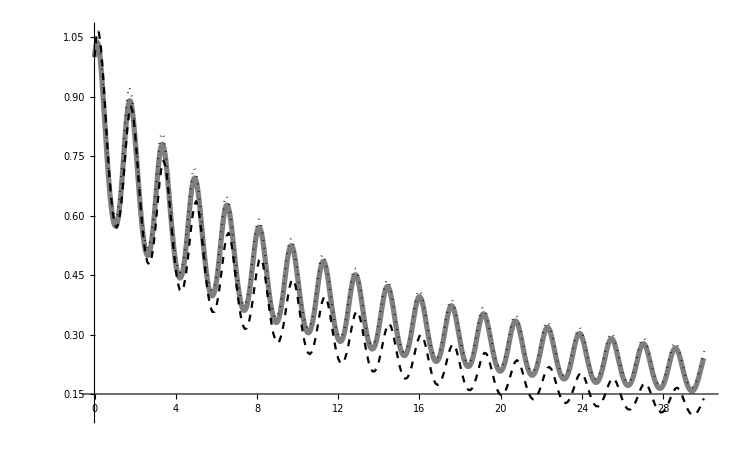

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

Ab3PlotCompare.jpg

```mathematica
h=0.1;u0=1;xbig=30;num=Floor[xbig/h];
g[x_,u_]=u*Cos[4x+u];
s=NDSolve[{u'[x]==g[x,u[x]],u[0]==1},u,{x,0,30}];
NDSolvePlot=Plot[Evaluate[u[x]/.s],{x,0,xbig},PlotRange->All,PlotStyle->{Thickness[0.005],Opacity[0.5],Black}];


Euler1[{x_,u_}]={x+h,u+h*g[x,u]};
Euler1s=NestList[Euler1,{0,u0},num];
Euler1Plot=ListPlot[Euler1s,PlotStyle->{PointSize[0.005],Black,Dashed},Joined->True,PlotRange->All];

Euler1PlotCompare=Show[Euler1Plot,NDSolvePlot];

SetDirectory[NotebookDirectory[]];
Export["Euler1Plot.jpg",Euler1PlotCompare,ImageResolution->400];
AB3[{x_,u_,u1_,u2_}]={x+h,u+h/12(23g[x,u]-16g[x-h,u1]+5g[x-2h,u2]),u,u1};
xin=2h;u2in=u0;u1in=u2in+h*g[0,u2in];uin=u1in+h*g[h,u1in];
in={xin,uin,u1in,u2in};


AB3out=NestList[AB3,in,num];
AB3s=Table[{AB3out[[i,1]],AB3out[[i,2]]},{i,1,num}];
AB3Plot=ListPlot[AB3s,PlotStyle->{PointSize[0.005],Dotted,Black},Joined->True,PlotRange->All];
AB3PlotCompare=Show[NDSolvePlot,AB3Plot,Euler1Plot]
SetDirectory[NotebookDirectory[]]
Export["Ab3PlotCompare.jpg",AB3PlotCompare,ImageResolution->1000]
```

## (*Boundary Value Problem*)

(-9 π^2+36 π^2 x+9 π^2 x^4-32 Sin[6 π x])/(36 π^2)

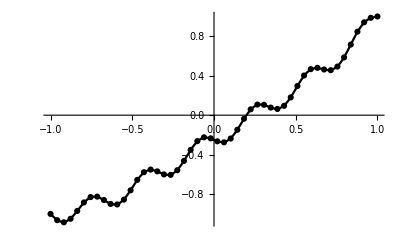

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

bvp1d.jpg

```mathematica
b1=-1;b2=1;
ρ[x_]=32Sin[6Pi*x]+3 x^2;
s=DSolve[{y''[x]==ρ[x],y[-1]==b1,y[1]==b2},y,x];
ϕexact[x_]=y[x]/.s[[1]]
exactplot=Plot[ϕexact[x],{x,-1,1},PlotStyle->Black];

num=50;h=2/(num-1);
X[i_]=-1+h*(i-1);
dist[i_,j_]=Norm[X[i]-X[j]];
(*Table[X[i],{i,1,num}];*)



JJ[i_]=Piecewise[{
{b1,X[i]==-1},
{b2,X[i]==1},
{h^2 ρ[X[i]],True}
}];
J=Table[N[JJ[i]],{i,1,num}];

Interior[i_]=If[X[i]==-1||X[i]==1,0,1];
(*Table[Interior[i],{i,1,num}];*)

M=SparseArray[{
{i_,i_}->(1-Interior[i])-2Interior[i],
{i_,j_}/;dist[i,j]==h->Interior[i]
},{num,num}];
M//MatrixForm;

ϕs=LinearSolve[M,J];
data=Table[{N[X[i]],ϕs[[i]]},{i,1,num}];
numplot=ListPlot[data,PlotStyle->Black];
compareplot=Show[exactplot,numplot]
SetDirectory[NotebookDirectory[]]
Export["bvp1d.jpg",compareplot,ImageResolution->400]
```

```mathematica
(*The Heat Equation*)
```

### (*Stability*)

(1-4 α+4 α θ)/(1+4 α θ)

{{α→-1/(2 (-1+2 θ))}}

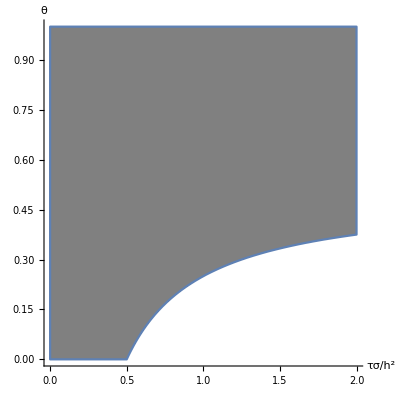

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

StableRegion.jpg

```mathematica
stab[α_,θ_]=λ/.Solve[λ==1-4α((1-θ)+θ*λ),λ][[1]]

Solve[stab[α,θ]==-1,α]
StableRegion=RegionPlot[-1<stab[α,θ]<1,{α,0,2},{θ,0,1},AxesLabel->{"τσ/h^2","θ"},Axes->True,Frame->None,PlotStyle->Gray]
SetDirectory[NotebookDirectory[]]
Export["StableRegion.jpg",StableRegion,ImageResolution->400]
```

0

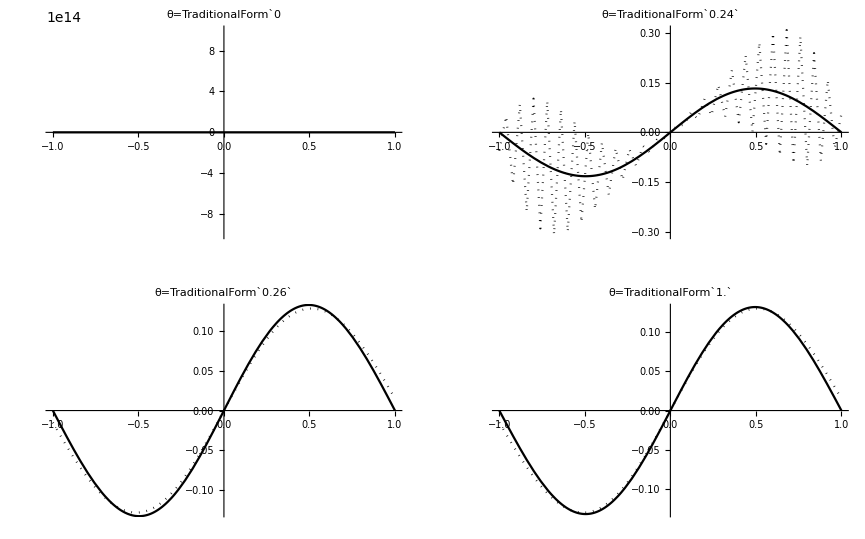

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

ImplicitPlot.jpg

```mathematica
Clear[uin]
num=50;h=2/num;safety =2;τ=safety 1/2 h^2;
uin[x_]=Sin[Pi*x]+3*Sin[2Pi*x];
u[t_,x_]=Exp[-Pi^2 t]Sin[Pi*x]+Exp[-4 Pi^2 t]3*Sin[2Pi*x];
Plot[u[0,x],{x,-1,1}];
Simplify[D[u[t,x],t]-D[u[t,x],{x,2}]]
ExactPlot=Plot[u[128τ,x],{x,-1,1},PlotStyle->Black];

Lap=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{num+1,num+1}];
MatrixForm[Lap];

xs=Table[-1+j*h,{j,0,num}];
usin=N[uin[xs]];



θ=0;
Step[u_]:=LinearSolve[IdentityMatrix[num+1]-θ*τ/h^2 Lap,u+(1-θ)τ/h^2 Lap.u]
Soln=Table[{xs[[j]],Nest[Step,usin,128][[j]]},{j,1,num+1}];
SolnPlot=ListPlot[Soln,Joined->True,PlotStyle->{Dotted,Black},PlotRange->All,PlotLabel->Pane[StringForm["θ=`1`",θ],Alignment->{Bottom,Right},ImageSize->270],ImageSize->400];
P1=Show[SolnPlot,ExactPlot];

θ=0.24;
Step[u_]:=LinearSolve[IdentityMatrix[num+1]-θ*τ/h^2 Lap,u+(1-θ)τ/h^2 Lap.u]
Soln=Table[{xs[[j]],Nest[Step,usin,128][[j]]},{j,1,num+1}];
SolnPlot=ListPlot[Soln,Joined->True,PlotStyle->{Dotted,Black},PlotRange->All,PlotLabel->StringForm["θ=`1`",θ]];
P2=Show[SolnPlot,ExactPlot];
θ=0.26;
Step[u_]:=LinearSolve[IdentityMatrix[num+1]-θ*τ/h^2 Lap,u+(1-θ)τ/h^2 Lap.u]
Soln=Table[{xs[[j]],Nest[Step,usin,128][[j]]},{j,1,num+1}];
SolnPlot=ListPlot[Soln,Joined->True,PlotStyle->{Dotted,Black},PlotRange->All,PlotLabel->StringForm["θ=`1`",θ]];
P3=Show[SolnPlot,ExactPlot];
θ=1.0;
Step[u_]:=LinearSolve[IdentityMatrix[num+1]-θ*τ/h^2 Lap,u+(1-θ)τ/h^2 Lap.u]
Soln=Table[{xs[[j]],Nest[Step,usin,128][[j]]},{j,1,num+1}];
SolnPlot=ListPlot[Soln,Joined->True,PlotStyle->{Dotted,Black},PlotRange->All,PlotLabel->StringForm["θ=`1`",θ]];
P4=Show[SolnPlot,ExactPlot];
ImplicitPlot=GraphicsGrid[{{P1,P2},{P3,P4}}]
SetDirectory[NotebookDirectory[]]
Export["ImplicitPlot.jpg",ImplicitPlot,ImageResolution->400]
```

## (*Poisson Equation in Two Dimensions*)

```mathematica
(*b1=-1;b2=1;
ρ[x_]=32Sin[6Pi*x]+3x;
s=DSolve[{y''[x]==ρ[x],y[-1]==b1,y[1]==b2},y,x];
ϕexact[x_]=y[x]/.s[[1]];
exactplot=Plot[ϕexact[x],{x,-1,1},PlotStyle->Black];
*)
ϕ[x_,y_]=Sinh[Pi*x]Sin[Pi*y]+3*Sin[Pi*x]Sin[2*Pi*y];

b1[y_]=ϕ[-1,y]
b2[y_]=ϕ[1,y]
b3[x_]=ϕ[x,-1]
b4[x_]=ϕ[x,1]
ρ[x_,y_]=D[ϕ[x,y],{x,2}]+D[ϕ[x,y],{y,2}];
Simplify[ρ[x,y]]
exactplot3D=Plot3D[ϕ[x,y],{x,-1,1},{y,-1,1},PlotRange->All,PlotLabel->"Poisson",PlotStyle->GrayLevel[0.7,0.5],Boxed->False,Mesh->None];

num=16;h=2/(num-1);
X[i_]=-1.+h*Mod[i-1,num];
Y[i_]=-1.+h*Quotient[i-1,num];
ϕs=Table[Chop[ϕ[X[i],Y[i]]],{i,1,num^2}];
dist[i_,j_]=Norm[{X[i],Y[i]}-{X[j],Y[j]}];
Table[Y[i],{i,1,num^2}];


JJ[i_]=Piecewise[{
{b1[Y[i]],X[i]==-1},
{b2[Y[i]],X[i]==1},
{b3[X[i]],Y[i]==-1},
{b4[X[i]],Y[i]==1},
{h^2 ρ[X[i],Y[i]],True}
}];
J=Table[Chop[N[JJ[i]]],{i,1,num^2}];


Interior[i_]=If[X[i]==-1||X[i]==1||Y[i]==-1||Y[i]==1,0,1];
M=SparseArray[{
{i_,i_}->(1-Interior[i])-4Interior[i],
{i_,j_}/;Abs[i-j]==1||Abs[i-j]==num->Interior[i]
},{num^2,num^2}];
(*Table[Interior[i],{i,1,num^2}];*)
(*M//MatrixForm;*)

Norm[M.ϕs-J]

ϕs=LinearSolve[M,J];
data=Table[{N[X[i]],Y[i],ϕs[[i]]},{i,1,num^2}];
numplot3D=ListPointPlot3D[data,PlotRange->All,PlotLabel->"Numerical",PlotStyle->{PointSize[0.0125],Black},Boxed->False];
PoissonPlot=Show[exactplot3D,numplot3D]
SetDirectory[NotebookDirectory[]];
Export["PoissonPlot.jpg",PoissonPlot,ImageResolution->400]
```

-Sin[π y] Sinh[π]

Sin[π y] Sinh[π]

0

0

-15 π^2 Sin[π x] Sin[2 π y]

0.97971

-Graphics3D-

PoissonPlot.jpg

## (*Radial Basis Functions*)

{-0.135063,0.545861,0.886971,-0.974054,-0.250683,-0.273247,-0.697446,0.177878,0.00928936,0.49141}

{0.0301032,0.757652,0.759615,-0.786978,-0.612229,-0.554808,-0.726932,-0.0207885,0.199023,0.495378}

{2.42905,-7.94366,15.0807,-16.5884,11.2715,-4.46782,-1.9456,4.19757,-3.66759,2.1159}

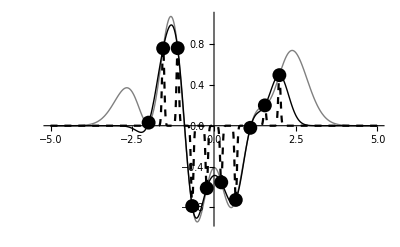

RBFCompPlot.jpg

```mathematica
Clear[ϵ,num,xs,fs,dataplot,ϕ,Φ,cs,polate,polateplot1,dataplot,polateplot2] 
num=10;
(*xs=Table[N[x],{x,-2,2,4/(num-1)}];*)
xs={-2.,-1.5555555555555556,-1.1111111111111112,-0.6666666666666666,-0.2222222222222222,0.2222222222222222,0.6666666666666666,1.1111111111111112,1.5555555555555556,2.};
(*xs=Table[RandomReal[{-2,2}],{x,-2,2,4/(num-1)}];*)
Dimensions[xs];
fs=RandomReal[{-1,1},num];
dataplot=ListPlot[Table[{xs[[i]],fs[[i]]},{i,1,num}],PlotStyle->{Black,PointSize[0.025]}];

 ϵ=num/4;
ϕ[x_]=Exp[-ϵ^2*x^2]; 
Φ=Table[ϕ[xs[[i]]-xs[[j]]],{i,1,num},{j,1,num}];
cs=LinearSolve[Φ,fs]
polate[x_]=Sum[cs[[i]]ϕ[x-xs[[i]]],{i,1,num}];
(*dataplot=ListPlot[Table[{xs[[i]],fs[[i]]},{i,1,num}],PlotStyle->Red];*)
polateplot1=Plot[polate[x],{x,-5,5},PlotRange->All,PlotStyle->{Thick,Black}];
Show[polateplot1,dataplot];
 ϵ=8 num/4;
ϕ[x_]=Exp[-ϵ^2*x^2]; 
Φ=Table[ϕ[xs[[i]]-xs[[j]]],{i,1,num},{j,1,num}];
cs=LinearSolve[Φ,fs]
polate[x_]=Sum[cs[[i]]ϕ[x-xs[[i]]],{i,1,num}];
(*dataplot=ListPlot[Table[{xs[[i]],fs[[i]]},{i,1,num}],PlotStyle->Red];*)
polateplot2=Plot[polate[x],{x,-5,5},PlotRange->All,PlotStyle->{Dashed,Black}];
ϵ=1/2 num/4;
ϕ[x_]=Exp[-ϵ^2*x^2]; 
Φ=Table[ϕ[xs[[i]]-xs[[j]]],{i,1,num},{j,1,num}];
cs=LinearSolve[Φ,fs]
polate[x_]=Sum[cs[[i]]ϕ[x-xs[[i]]],{i,1,num}];
(*dataplot=ListPlot[Table[{xs[[i]],fs[[i]]},{i,1,num}],PlotStyle->Red];*)
polateplot3=Plot[polate[x],{x,-5,5},PlotRange->All,PlotStyle->{Thick,Gray}];
RBFCompPlot=Show[polateplot3,polateplot2,polateplot1,dataplot]
SetDirectory[NotebookDirectory[]];
Export["RBFCompPlot.jpg",RBFCompPlot,ImageResolution->400]
```

## (*Dynamical Systems*)

## (*Cat Homoclinic Tangle *)

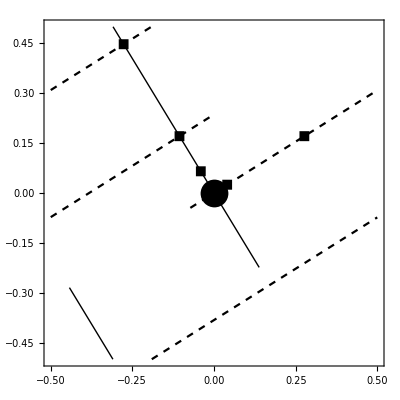

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

CatHomoclinicTangle.jpg

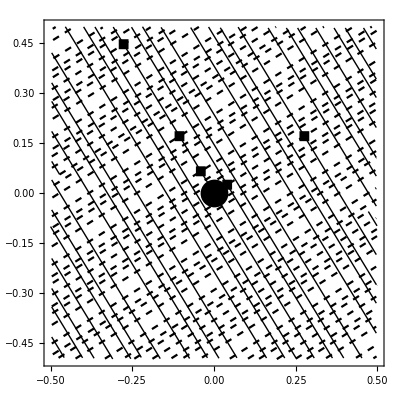

CatHomoclinicTangleLong.jpg

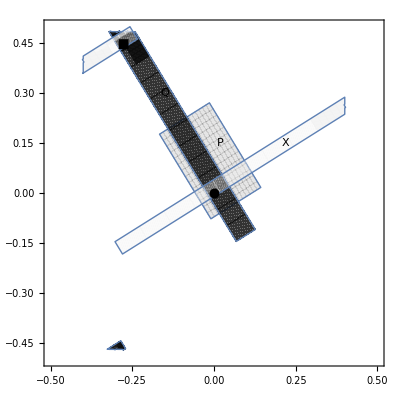

CatHorseShoe.jpg

```mathematica
catmatrix={{2,1},{1,1}};
Inverse[catmatrix];

cat[x_]:={fund[2x[[1]]+x[[2]]],fund[x[[1]]+x[[2]]]}
catinverse[x_]:={fund[x[[1]]-x[[2]]],fund[-x[[1]]+2x[[2]]]}
pt={RandomReal[{-0.5,0.5}],RandomReal[{-0.5,0.5}]};
cat[pt];
cat[catinverse[pt]];
stablevector={-1+1/2 (3-√5),1};
unstablevector={-1+1/2 (3+√5),1};
Simplify[catmatrix.stablevector-(3-√5)/2 stablevector];
Simplify[catmatrix.unstablevector-(3+√5)/2 unstablevector];

fund[x_]=-0.5+SawtoothWave[x+0.5];
(*Plot[fund[x],{x,-1.5,1.5}]*)

stablemanifold[t_]:={fund[stablevector[[1]]*t],fund[stablevector[[2]]*t]};


unstablemanifold[t_]:={fund[unstablevector[[1]]*t],fund[unstablevector[[2]]*t]};

fixedpt={0,0};
plotfixedpt=Graphics[{Black,PointSize[0.05],Point[fixedpt]}];

T=1.571;

homoclinictime1=1/(√5);
homoclinictime2=-1/(√5);
homoclinicpt1=stablemanifold[homoclinictime1];
homoclinicpt2=unstablemanifold[homoclinictime2];

pt2=cat[homoclinicpt1];
pt3=catinverse[homoclinicpt1];
pt4=Nest[cat,homoclinicpt1,2];
pt5=Nest[catinverse,homoclinicpt1,3];
(*plothomoclinicpt1=Graphics[{Purple,PointSize[0.03],Point[homoclinicpt1]}];*)

(*plothomoclinicpt1=Graphics[Rectangle[homoclinicpt1-{0.015,0.015},homoclinicpt1+{0.015,0.015}]];*)
plotRect[x_]:=Graphics[Rectangle[x-{0.015,0.015},x+{0.015,0.015}]];
plothomoclinicpt1=plotRect[homoclinicpt1];

plotpt2=plotRect[pt2];
plotpt3=plotRect[pt3];
plotpt4=plotRect[pt4];
plotpt5=plotRect[pt5];
N[2.75*homoclinictime1];
stablemanifold[0.28];
plotstable=ParametricPlot[stablemanifold[t],{t,-0.5*homoclinictime1,1.6*homoclinictime1},Frame->True,PlotStyle->{Thick,Black},Axes->None,AspectRatio->1,PlotRange->{{-0.5,0.5},{-0.5,0.5}}];

plotunstable=ParametricPlot[unstablemanifold[t],{t,-0.1*homoclinictime1,2.75*homoclinictime1},Frame->True,PlotStyle->{Dashed, Black},Axes->None,PlotLabel->"Stable=Blue,Unstable=Red",PlotRange->{{-0.5,0.5},{-0.5,0.5}}];
CatHomoclinicTangle=Show[plotstable,plotunstable,plotfixedpt,plothomoclinicpt1,plotpt2,plotpt3,plotpt4,plotpt5]
SetDirectory[NotebookDirectory[]]
Export["CatHomoclinicTangle.jpg",CatHomoclinicTangle,ImageResolution->400]

plotstablelong=ParametricPlot[stablemanifold[t],{t,-20*homoclinictime1,20*homoclinictime1},Frame->True,PlotStyle->{Thick,Black},Axes->None,AspectRatio->1,PlotRange->{{-0.5,0.5},{-0.5,0.5}}];

plotunstablelong=ParametricPlot[unstablemanifold[t],{t,-20*homoclinictime1,20*homoclinictime1},Frame->True,PlotStyle->{Dashed, Black},Axes->None,PlotLabel->"Stable=Blue,Unstable=Red",PlotRange->{{-0.5,0.5},{-0.5,0.5}}];
CatHomoclinicTangleLong=Show[plotstablelong,plotunstablelong,plotfixedpt,plothomoclinicpt1,plotpt2,plotpt3,plotpt4,plotpt5]
Export["CatHomoclinicTangleLong.jpg",CatHomoclinicTangleLong,ImageResolution->400]

dist[x_]:=√((x[[1]])^2+(x[[2]])^2);
dist[{1,2}];
h2={-0.27639320225002106,0.44721359549995787};
forw=NestList[cat,h2,15];
forwdist=Table[dist[forw[[i]]],{i,1,15}];

back=NestList[catinverse,h2,15];
backdist=Table[dist[back[[i]]],{i,1,15}];
d=Min[backdist];
m=4;
n=Position[backdist,Min[backdist]][[1,1]]-1;
dist[Nest[cat,h2,m]];
dist[Nest[catinverse,h2,n]];

d=1.22*10^-1;
m=2;
n=1;
sv=N[stablevector/Norm[stablevector]];
uv=N[unstablevector/Norm[unstablevector]];
{x1,x2}={-0.5d,1.95d};{y1,y2}={-0.4d,1.07*d};
P=ParametricPlot[x*sv+y*uv,{x,x1,x2},{y,y1,y2},AspectRatio->1,PlotRange->{{-0.5,0.5},{-0.5,0.5}},PlotStyle->Directive[Opacity[0.1],Black]];
Q=ParametricPlot[Nest[catinverse,x*sv+y*uv,n],{x,x1,x2},{y,y1,y2},AspectRatio->1,PlotRange->{{-0.5,0.5},{-0.5,0.5}},RegionFunction->(-0.47<#2<0.485&),PlotStyle->Directive[Opacity[0.6],GrayLevel[0.05]]];
X=ParametricPlot[Nest[cat,x*sv+y*uv,m],{x,x1, x2},{y,y1,y2},AspectRatio->1,PlotRange->{{-0.5,0.5},{-0.5,0.5}},RegionFunction->(-0.4<#1<0.4&),PlotStyle->Directive[Opacity[0.2],GrayLevel[0.95]]];

plotfixedpt=Graphics[{Disk[fixedpt,0.015],Text["X",{0.22,0.15}],Text["P",{0.02,0.15}]}];
plothomoclinicpt1=Graphics[{Rectangle[homoclinicpt1-{0.015,0.015},homoclinicpt1+{0.015,0.015}],Text["Q",{-0.15,0.3}]}];
CatHorseShoe=Show[P,Q,X,plotfixedpt,plothomoclinicpt1]
Export["CatHorseShoe.jpg",CatHorseShoe,ImageResolution->400]
```

## Explicit Horse Shoe

Set::write: Tag Rational in 2/15[X_, Y_] is Protected.

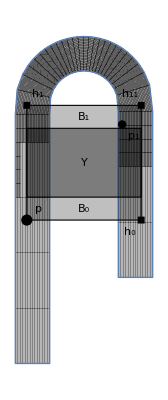

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

ExplicitHorseShoe.jpg

```mathematica
ξ[y_]=-1/2+(-1+y)/(-2+λ);
s[x_]=1-2x;
g[x_,y_]=Piecewise[{
{{x,y},y<=1},
{{1/2,1}+s[x]{ξ[y],√(1/4-ξ[y]^2)},1≤y<=λ-1},
{{1-x,λ-y},λ-1≤y},
{{0,0},True}
}];

h[X_,Y_]=Piecewise[{
{{X,Y},X<=1},
{{1,1/2}+s[Y]{√(1/4-ξ[X]^2),ξ[X]},1≤X<=λ-1},
{{λ-X,1-Y},λ-1≤X},
{{0,0},True}
}];

ρ1[X_,Y_]=2 √((X-1/2)^2+(Y-1)^2);
η1[X_,Y_]=(X-1/2)/ρ1[X,Y];
ψ[{X_,Y_}]=Piecewise[{
{h[λ*X,λ^-1 Y],Y<1},
{{λ/2(1-ρ1[X,Y]),1/2+(1-2/λ)η1[X,Y]},1<Y}
}];

ρ2[x_,y_]=2 √((x-1)^2+(y-1/2)^2);
η2[x_,y_]=(y-1/2)/ρ2[x,y];
ϕ[{x_,y_}]=Piecewise[{
{g[λ^-1 x,λ*y],x<=1},
{{(1-2/λ)η2[x,y]+1/2,λ/2(1-ρ2[x,y])},1<x},
{{0,0},True}

}];
Simplify[ϕ[{x,y}]];

λ=5.0;





h1={0,1};
h0={1,0};
h11={1,1};
p={0,0};
p1={1/(1+λ^-1),1/(1+λ^-1)};
ϕ[q];
ϕ[ϕ[ϕ[h1]]];
NestList[ϕ,h1,15];
NestList[ψ,h0+{0.001,0.001},15];
Wu=ParametricPlot[ϕ[{0.0001,y}],{y,-0.25,1.099},Exclusions->None,PlotStyle->Red,PlotRange->All,Axes->None,Frame->False];
Ws=ParametricPlot[ψ[{X,0.001}],{X,-0.25,1.0999},Exclusions->None,PlotLabel->ψ,PlotStyle->Blue,PlotRange->All,Axes->None,Frame->False];

forwbig=ParametricPlot[ϕ[{x,y}],{x,-0.5,1.},{y,-0.25,1.0999},Exclusions->None,PlotStyle->GrayLevel[0.05],PlotRange->All,Axes->None,Frame->False];
backwbig=ParametricPlot[ψ[{X,Y}],{X,-0.25,1.0999},{Y,-1,1.0000},Exclusions->None,PlotLabel->ψ,PlotStyle->GrayLevel[0.5],PlotRange->All,Axes->None];
square=Graphics[{
(*{EdgeForm[Directive[Dashed,Black]],White,{Opacity[0.0],Rectangle[{-0.3,-0.35},{1.2,1.3}]}},*)
Text["B_0",{0.5,0.1}],
Text["B_1",{0.5,1-0.1}],
Text["Y",{0.5,0.5}],
{PointSize[0.02],Point[p]},
Text["p",{0,0}+{0.1,0.1}],
{PointSize[0.015],Point[p1]},
Text["p_1",p1+{0.1,-0.1}],
(*{PointSize[0.025],Purple,Point[h0]},*)
Rectangle[h0-{0.03,0.03},h0+{0.03,0.03}],
Text["h_0",h0-{0.1,0.1}],
Rectangle[h1-{0.03,0.03},h1+{0.03,0.03}],
(*{PointSize[0.025],Purple,Point[h1]},*)
Text["h_1",{0,1}+{0.1,0.1}],
(*{PointSize[0.025],Purple,Point[h11]},*)
Rectangle[h11-{0.03,0.03},h11+{0.03,0.03}],
Text["h_11",{1,1}+{-0.1,0.1}],
{EdgeForm[Directive[Thick,Black]],Black,{Opacity[0.35],Rectangle[{0,λ^-1},{1.0,1.0-λ^-1}]}},
{EdgeForm[Directive[Thick,Black]],Black,{Opacity[0.25],Rectangle[{0,0},{1.0,1.0}]}}
}];
ExplicitHorseShoe=Show[forwbig,backwbig,square]
SetDirectory[NotebookDirectory[]]
Export["ExplicitHorseShoe.jpg",ExplicitHorseShoe,ImageResolution->400]
```

## Periodic Orbit of a Binary Sequence

{5/16-x/576,410-500 y}

{180/577,410/501}

Piecewise[{{{x/3,2 y}, y<1/2}, {{1-x/4,5 (1-y)}, 4/5<y}, {0, True}}]

{{180/577,410/501},{532/577,455/501},{444/577,230/501},{148/577,460/501},{540/577,205/501},{180/577,410/501},{532/577,455/501}}

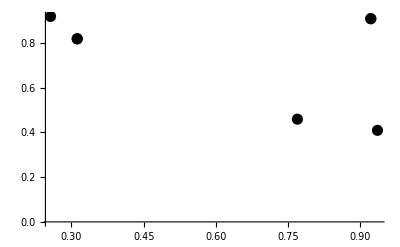

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

OrbitBinarySequence.jpg

```mathematica
μ0=1/3;μ1=1/4;ν0=1/2;ν1=1/5;
A0[{x_,y_}]={μ0*x,ν0^-1 y};
A1[{x_,y_}]={1-μ1*x,1/ν1(1-y)};
As[{x_,y_}]=Simplify[A0[A1[A0[A1[A1[{x,y}]]]]]]
{xs,ys}=First[{x,y}/.Solve[As[{x,y}]=={x,y},{x,y}]]
A[{x_,y_}]=Piecewise[{{A0[{x,y}],y<ν0},{A1[{x,y}],1-ν1<y}}
]
OrbitBinarySequence=NestList[A,{xs,ys},6]
PlotOrbitBinarySequence=ListPlot[OrbitBinarySequence,PlotStyle->{PointSize[0.02],Black}]
SetDirectory[NotebookDirectory[]]
Export["OrbitBinarySequence.jpg",PlotOrbitBinarySequence,ImageResolution->400]
```

## Chaotic Advection

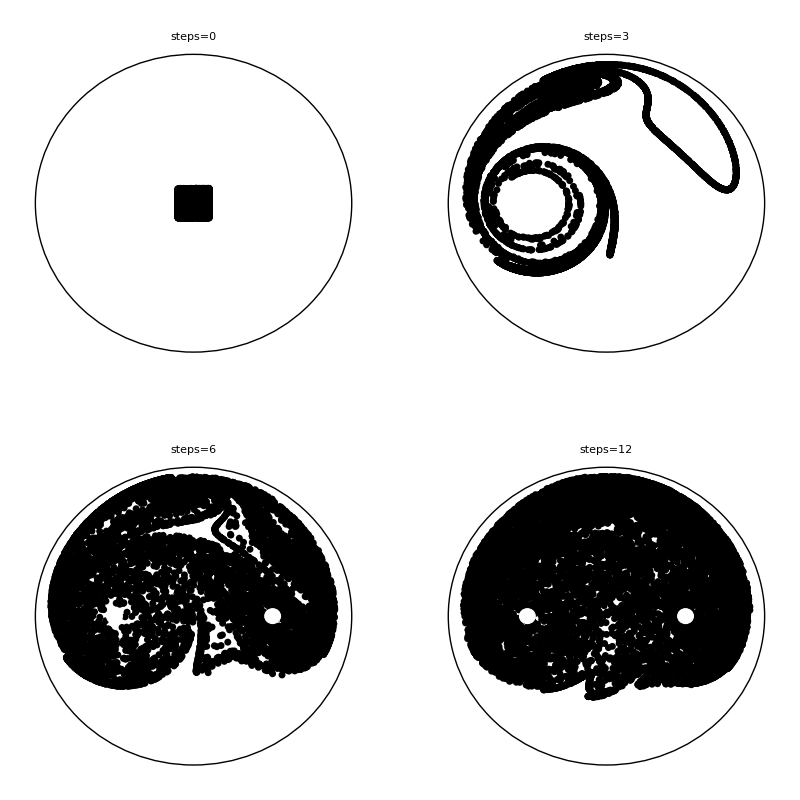

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

ArefPlots.jpg

```mathematica
Clear[z0,zc,r,ϕ,f1]
Off[FindRoot::"lstol"]
r1=Random[];
θ1=2Pi*Random[];
a=1;

β=0.5;
μ=2;
ζ=β+I*0;
z0=r1*Exp[I*θ1];
mζ=a^2/Conjugate[ζ];
t=μ/2;
f1[z_]:=
Module[{z0=z,λ,zc,r,ϕ},
λ=Abs[(z0-ζ)/(z0-mζ)];
zc=(ζ-λ^2*mζ)/(1-λ^2);
r=λ/(1-λ^2)Abs[mζ-ζ];
ϕ=FindRoot[ϕ1-(2λ)/(1+λ^2) Sin[ϕ1]-1/r^2(1-λ^2)/(1+λ^2)t,{ϕ1,0}][[1,2]];

Return[zc+(z0-zc)*Exp[I*ϕ]]
]
f2[z_]:=
Module[{z0=z,λ,zc,r,ϕ},
λ=Abs[(z0+ζ)/(z0+mζ)];
zc=-(ζ-λ^2*mζ)/(1-λ^2);
r=λ/(1-λ^2)Abs[mζ-ζ];
ϕ=FindRoot[ϕ1-(2λ)/(1+λ^2) Sin[ϕ1]-1/r^2(1-λ^2)/(1+λ^2)t,{ϕ1,0}][[1,2]];

Return[zc+(z0-zc)*Exp[I*ϕ]]
]
f[z_]:=f2[f1[z]]

inpt={Random[],Random[]};

(*Fixed point by the secant method*)

g[z_]:=f[z]-z
F[u_]:={u[[2]],u[[2]]-g[u[[2]]](u[[2]]-u[[1]])/(g[u[[2]]]-g[u[[1]]])}
pt1=-0.14038754952831803+0.990096629596038 ⅈ+10^-4*Random[]*Exp[I*2Pi*RandomReal[{-1,1}]];
pt2=pt1+10^-2*Random[]*Exp[I*2Pi*RandomReal[{-1,1}]];
inpts={pt1,pt2};
Take[NestList[F,inpts,10^2],-10];

fixedpt=0.5894016741597633 ⅈ;
ϵ1=Random[]*10^-4;
ϵ2=Random[]*10^-5;
ϵ=ϵ1+I*ϵ2;
Jac={{Re[(f[fixedpt+ϵ1]-f[fixedpt])/ϵ1],Im[(f[fixedpt+ϵ1]-f[fixedpt])/ϵ1]},{Re[(f[fixedpt+I*ϵ2]-f[fixedpt])/ϵ2],Im[(f[fixedpt+I*ϵ2]-f[fixedpt])/ϵ2]}};
Jac//MatrixForm;
Det[Jac];
Eigenvalues[Jac];
MatrixForm[Jac.Transpose[Jac]];
Eigenvalues[Jac.Transpose[Jac]];
N[13.2664*0.0753655];

(*Aref Plots*)
stirrer1=Graphics[{EdgeForm[Thick],White, Disk[{Re[ζ],Im[ζ]},0.05]}];
stirrer2=Graphics[{EdgeForm[Thick],White, Disk[{-Re[ζ],-Im[ζ]},0.05]}];
fixed=Graphics[{Green, Disk[{Re[fixedpt],Im[fixedpt]},0.025]}];


num=10^4;sizebox=0.1;
centerbox=0.0;
inpts=Table[centerbox+sizebox(RandomReal[{-1,1}]+I*RandomReal[{-1,1}]),{i,1,num}];


steps=0;
complexpts=Table[Nest[f,inpts[[i]],steps],{i,1,num}];
pts=Table[{Re[complexpts[[i]]],Im[complexpts[[i]]]},{i,1,num}];
label=StringJoin[ToString["steps="],ToString[steps]];
ArefPlot0=Show[Graphics[{PointSize[0.0125],Point[pts]}],Graphics[Circle[]],stirrer1,stirrer2,PlotLabel->label];
steps=3;
complexpts=Table[Nest[f,inpts[[i]],steps],{i,1,num}];
pts=Table[{Re[complexpts[[i]]],Im[complexpts[[i]]]},{i,1,num}];
label=StringJoin[ToString["steps="],ToString[steps]];
ArefPlot3=Show[Graphics[{PointSize[0.0125],Point[pts]}],Graphics[Circle[]],stirrer1,stirrer2,PlotLabel->label];
steps=6;
complexpts=Table[Nest[f,inpts[[i]],steps],{i,1,num}];
pts=Table[{Re[complexpts[[i]]],Im[complexpts[[i]]]},{i,1,num}];
label=StringJoin[ToString["steps="],ToString[steps]];
ArefPlot6=Show[Graphics[{PointSize[0.0125],Point[pts]}],Graphics[Circle[]],stirrer1,stirrer2,PlotLabel->label];

steps=12;
complexpts=Table[Nest[f,inpts[[i]],steps],{i,1,num}];
pts=Table[{Re[complexpts[[i]]],Im[complexpts[[i]]]},{i,1,num}];
label=StringJoin[ToString["steps="],ToString[steps]];
ArefPlot12=Show[Graphics[{PointSize[0.0125],Point[pts]}],Graphics[Circle[]],stirrer1,stirrer2,PlotLabel->label];

ArefPlots=GraphicsGrid[{{ArefPlot0,ArefPlot3},{ArefPlot6,ArefPlot12}}]
SetDirectory[NotebookDirectory[]]
Export["ArefPlots.jpg",ArefPlots,ImageResolution->400]





(*complexpts2=NestList[f2,0.12+0.31*I,104];
pts2=Table[{Re[complexpts2[[i]]],Im[complexpts2[[i]]]},{i,1,104}];
pts=Join[pts1,pts2];
Graphics[Point[pts]]
*)
```

```mathematica
One Dimensional IsingModel
```

Dimensional IsingModel One

{1/2 ⅇ^(-B-J) (ⅇ^(2 J)+ⅇ^(2 (B+J))-√(4 ⅇ^(2 B)+ⅇ^(4 J)+ⅇ^(4 (B+J))-2 ⅇ^(2 B+4 J))),1/2 ⅇ^(-B-J) (ⅇ^(2 J)+ⅇ^(2 (B+J))+√(4 ⅇ^(2 B)+ⅇ^(4 J)+ⅇ^(4 (B+J))-2 ⅇ^(2 B+4 J)))}

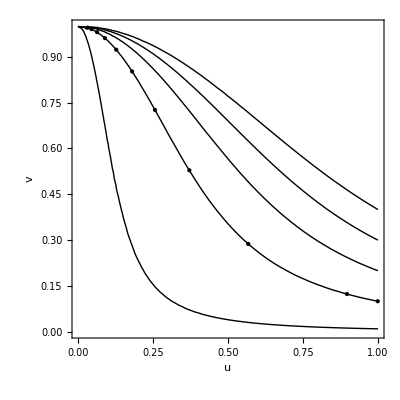

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

Ising1D.jpg

```mathematica
Clear[P,P0,J]
P=({{Exp[J+B], Exp[-J]}, {Exp[-J], Exp[J-B]}});
P0=({{1/(u*v), u}, {u, v/u}});
P0//MatrixForm;
Simplify[Eigenvalues[P]]
Assuming[u>0 && v>0,Simplify[Eigenvalues[P0]]];
Factor[Discriminant[1+(-2+4 u^4) y+y^2,y]];
Discriminant[1+(-2+4 u^4) y+y^2,y];
Factor[Discriminant[1+(-2+4 u^4) v^2+v^4,u]];
Factor[Solve[1+(-2+4 U) v^2+v^4==0,U][[1,1,2]]];
P0//MatrixForm;
P1=P0.P0;
P1//MatrixForm;
norm=Simplify[P1[[1,1]]P1[[1,2]]P1[[2,1]]P1[[2,2]]];
Q1=Assuming[u>0&&  v>0,Factor[P1/(norm)^(1/4)]];


λ2=Eigenvalues[P0][[1]];
λ1=Eigenvalues[P0][[2]];
ξ[u_,v_]=-Eigenvectors[P0][[1,1]];
Φ[u_,v_]=Log[Log[λ1/λ2]];
ContourPlot[ξ[u,v],{u,0,1},{v,0,1},Contours->15,ContourShading->None,ContourStyle->Thick,FrameLabel->Automatic];

f[{u_,v_}]={(v+1/v)^(1/2)/((u^4+u^-4+v^2+v^-2)^(1/4)),((u^4+v^2)^(1/2))/((u^4+v^-2)^(1/2))};

Orbit=NestList[f,{0.03182198850393857,0.995},10];

OrbitPlot=ListPlot[Orbit,PlotStyle->{Black,PointSize[Large]},PlotRange->All,AxesOrigin->{0,0}];
ξ[0.01,0.995];
contour=ContourPlot[ξ[u,v],{u,0,1},{v,0,1},Contours->{0.009973945042405176,0.1,0.2,0.3,0.4},ContourShading->None,ContourStyle->Thick,FrameLabel->Automatic, AxesLabel->{"u","v"}];
Ising1D=Show[contour,OrbitPlot]
SetDirectory[NotebookDirectory[]]
Export["Ising1D.jpg",Ising1D,ImageResolution->400]
```

```mathematica
Cayley Tree
```

Cayley Tree

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

CayleyTrees.jpg

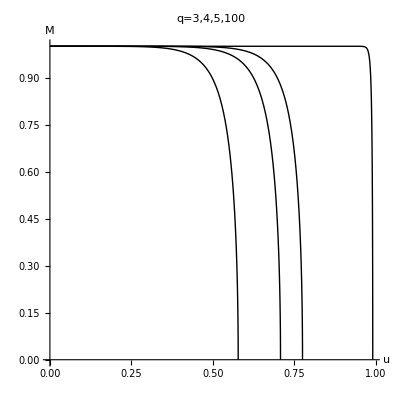

/Users/saradrajeev1/Dropbox/work/books/Rajeev/FluidsBookRajeev/Draft3/ImagesPrograms

IsingCayleySpMag.jpg

```mathematica
Clear[g]
g={0->1,0->2,0->3,1->11,1->12,2->21,2->22,3->31,3->32,11->111,11->112,12->121,12->122,21->211,21->212,22->221,22->222,31->311,31->312,32->321,32->322};
CayleyTree=TreePlot[g,Center,VertexLabeling->False,PlotStyle->{Thick,PointSize[Large],Black}];
(*SetDirectory[NotebookDirectory[]]
Export["CayleyTree.jpg",CayleyTree,ImageResolution->400]*)
g={0->1,0->2,1->11,1->12,2->21,2->22,11->111,11->112,12->121,12->122,21->211,21->212,22->221,22->222};
RootedCayleyTree=TreePlot[g,VertexLabeling->False,PlotStyle->{Thick,PointSize[Large],Black}];
CayleyTrees=GraphicsGrid[{{CayleyTree,RootedCayleyTree}}];
(*SetDirectory[NotebookDirectory[]]
Export["RootedCayleyTree.jpg",RootedCayleyTree,ImageResolution->400]*)
SetDirectory[NotebookDirectory[]]
Export["CayleyTrees.jpg",CayleyTrees,ImageResolution->400]
M[q_,x_]=(1-x^q)/(1+x^q);
u[q_,x_]=√(x*(1-x^(q-2))/(1-x^q));
u1[q_]=√((q-2)/q);
Simplify[Series[u[q,x],{x,1,2}]];
Simplify[Series[M[q,x],{x,1,2}]];
IsingCayleySpMag=ParametricPlot[{{u[3,x],M[3,x]},{u[4,x],M[4,x]},{u[5,x],M[5,x]},{u[100,x],M[100,x]}},{x,0,1},PlotStyle->{{Thick,Black}},PlotLabel->"q=3,4,5,100",AxesLabel->{u,M}]
SetDirectory[NotebookDirectory[]]
Export["IsingCayleySpMag.jpg",IsingCayleySpMag,ImageResolution->400]
```